# Basics

This notebook gives examples of the functions in GRQUICK.   First we load the package. 

To install the package go to:
1.) go to File->Install
2.) in the dialouge box that pops up select:
3.) Source->From File
4.) find and select the file GRQUICK.m
5.) In “Install Name” type in “GRQUICK.m

To load the package use the “<<” command below.

```mathematica
<<GRQUICKv4.m
```

The convention for this program follow Sean M. Carroll's (Spacetime and Geometry) and the indices run from 0 
to D-1.

While working do not use the variables GARRAY,RARRAY,RsARRAY, CHARRAY, SPEEDOFLIGHT.  

Type ?helpGRQUICK for a list of functions or ?Function for a function description.

More functions and improvements coming soon!!'

Here we load a list of functions and obtain information on the Ricci function.

```mathematica
?helpGRQUICK
```

To begin one must input a metric using Metin.  Type in ?Metin for usage.  For the usage of any function use ?function


Standard Differential Geometry objects are: Metric, IMetric, Christoffel,Riemann,
Weyl,Ricci,Rscalar,Einstein, Kretschmann, Metprod, Metnorm, Normalizevec, RaiseVector, LowerVector, CoordTransMet, CoordTransVec, and Setlight. 

Functions usefull for geodesic analysis are: Geodesics, Geoplot, Issol, ReplaceCoords


Functions which operate on tensore are: Coderv, and Tenstr.

Raychaudhuri functions are: SpatialMetric, BExpansion, ThetaExpansion, Shear, and Twist. 
The vector inputs to these function must be properly timelike normalized (I have not implemented a null formulation as of yet). For definitions 
see Wald's General Relativity text.


Important objects/tensors can be displayed using the commands: (GINV; GMET; DIM; COORDINATES)
,CHARRAY, GARRAY, RARRAY, RSARRAY, SPEEDOFLIGHT, and GEOSOL. 
These object are populated once the functions (Metin), Christoffel,
Einstein, Ricci, Rscalar, Setlight, and Geoplot have been computed respectively.

```mathematica
?Ricci
```

The Ricci tensor Ricci[i,j] = R_(ij\n)

The starting point of GRQUICK is to input a metric using “Metin”.  We first use the auto-loader and then we input our own spherically symmetric metric.

```mathematica
?Metin
```

For a dxd matrix g and d dimensional vector vec, Metin[g,vec] sets the working Metric to g and the coordinates to vec (default {t,x,y,z}). One can also use default metrics by inputing certain strings.  For a list of metrics type ?DefaultMet

The schwarchild metric can be loaded as

```mathematica
Metin["Schwar"]
```

Metric Success

A list of defualt metrics can be loaded using ?DefaultMet

```mathematica
?DefaultMet
```

The load decault metrics use Metin[string] with one of the following strings


Schwar = Schwarchild metric with COORDINATES={t,r,θ,ϕ} for a central mass of mass M;

FRW = Friedman walker metric with curvature k and coordinates {t,r,θ,ϕ} and expansion function a[t];

Reissner = Charged black hole with total charge q;

Kerr = rotating black hole with total angular momentum J;

Kerr-Newman = charged rotating black hole with charge q and angular momentum J;

DS static = Static desitter coordinates {t,r,θ,ϕ} with the cosmological horizon at r=α = √(3/Λ); 

DS universe = Desitter universe with a[t]=e^(H\ t) where H is the hubble constant;

DS-Schwar = De-sitter Schwarzchild metric where Λ is the cosmological constant and M is the mass of the black hole.

ADS = Anti-desitter for a spherical coordinate patch and ADS curvature k. 

ADS black hole = ADS black hole with ADS curvature k and mass-like parameter C;
 

ADS = Anti-desitter for a spherical coordinate patch and ADS curvature k. 

Note: we use geometrical units in which G=c=1.  The metrics are taken from Wikipedia and I make no claim to their accuracy.

Or we can use our own metric matrices

```mathematica
Metin[DiagonalMatrix[{a[t,x],b[t,x]}],{t,x}]
```

Metric Success

Note, dimension does not matter.  We shall focus on 4-d spherically symmetric space-times for now.

```mathematica
Metin[DiagonalMatrix[{m[t,r],n[t,r],r^2,r^2 Sin[θ]^2}],{t,r,θ,ϕ}]
```

Metric Success

Now that we have used “Metin” we can look at the metric tensor using GMET.

```mathematica
MatrixForm[GMET]
```

(m[t,r] | 0 | 0 | 0
0 | n[t,r] | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 Sin[θ]^2)

Similarly, “GINV” can be used to display all of the inverse metric.

```mathematica
GINV
```

{{1/m[t,r],0,0,0},{0,1/n[t,r],0,0},{0,0,1/r^2,0},{0,0,0,Csc[θ]^2/r^2}}

After a metric has been input we can calculate relevant geometric objects.  For example we calculate (Γ^0)_00

```mathematica
Christoffel[{{0},{0,0}}]
```

(m^(1,0)[t,r])/(2 m[t,r])

, and or (R^0)_101  (notice the index structure of the tensor!!!).

```mathematica
Riemann[{{0},{1,0,1}}]
```

(m[t,r] (m^(0,1)[t,r] n^(0,1)[t,r]+(n^(1,0)[t,r])^2)+n[t,r] ((m^(0,1)[t,r])^2+m^(1,0)[t,r] n^(1,0)[t,r]-2 m[t,r] (m^(0,2)[t,r]+n^(2,0)[t,r])))/(4 m[t,r]^2 n[t,r])

We can also obtain specific components of the metric and inverse metric using “Metric” and “Imetric”.

```mathematica
Metric[0,0]
```

m[t,r]

```mathematica
IMetric[0,0]
```

1/m[t,r]

We can also calculate the Ricci and Einstein tensors.

```mathematica
Simplify[Ricci[0,0]]
```

1/(4 r m[t,r] n[t,r]^2)(r n[t,r] ((m^(0,1)[t,r])^2+m^(1,0)[t,r] n^(1,0)[t,r])+m[t,r] (r (m^(0,1)[t,r] n^(0,1)[t,r]+(n^(1,0)[t,r])^2)-2 n[t,r] (2 m^(0,1)[t,r]+r (m^(0,2)[t,r]+n^(2,0)[t,r]))))

```mathematica
Einstein[0,0]
```

-(m[t,r] (-n[t,r]+n[t,r]^2+r n^(0,1)[t,r]))/(r^2 n[t,r]^2)

Rscalar gives the ricci scalar.

```mathematica
Rscalar
```

1/(2 r^2 m[t,r]^2 n[t,r]^2)(4 m[t,r]^2 (-n[t,r]+n[t,r]^2+r n^(0,1)[t,r])+r^2 n[t,r] ((m^(0,1)[t,r])^2+m^(1,0)[t,r] n^(1,0)[t,r])+r m[t,r] (r (m^(0,1)[t,r] n^(0,1)[t,r]+(n^(1,0)[t,r])^2)-2 n[t,r] (2 m^(0,1)[t,r]+r (m^(0,2)[t,r]+n^(2,0)[t,r]))))

If we wish we can display all of the einstein tensor as a NxN matrix using GARRAY.  Similar arrays exist for the other tensors as well but they can only be called either if 
1) said tensor has been computed or 
2) the Einstein tensor has been computed (see ?helpGRQUICK).

```mathematica
Simplify[GARRAY]
```

{{-(m[t,r] (-n[t,r]+n[t,r]^2+r n^(0,1)[t,r]))/(r^2 n[t,r]^2),(n^(1,0)[t,r])/(r n[t,r]),0,0},{(n^(1,0)[t,r])/(r n[t,r]),(m[t,r]-m[t,r] n[t,r]+r m^(0,1)[t,r])/(r^2 m[t,r]),0,0},{0,0,1/(4 m[t,r]^2 n[t,r]^2)r (-2 m[t,r]^2 n^(0,1)[t,r]-r n[t,r] ((m^(0,1)[t,r])^2+m^(1,0)[t,r] n^(1,0)[t,r])+m[t,r] (-r (m^(0,1)[t,r] n^(0,1)[t,r]+(n^(1,0)[t,r])^2)+2 n[t,r] (m^(0,1)[t,r]+r (m^(0,2)[t,r]+n^(2,0)[t,r])))),0},{0,0,0,1/(4 m[t,r]^2 n[t,r]^2)r Sin[θ]^2 (-2 m[t,r]^2 n^(0,1)[t,r]-r n[t,r] ((m^(0,1)[t,r])^2+m^(1,0)[t,r] n^(1,0)[t,r])+m[t,r] (-r (m^(0,1)[t,r] n^(0,1)[t,r]+(n^(1,0)[t,r])^2)+2 n[t,r] (m^(0,1)[t,r]+r (m^(0,2)[t,r]+n^(2,0)[t,r]))))}}

GRQUICK can also perform basic operations on contravariant vectors. For example, the norm of the position vector:

```mathematica
Metnorm[{t,r,θ,ϕ}]
```

r^2 θ^2+t^2 m[t,r]+r^2 n[t,r]+r^2 ϕ^2 Sin[θ]^2

The scalar product of two contravariant vectors is:

```mathematica
Metprod[{a,b,c,d},{t,r,θ,ϕ}]
```

c r^2 θ+a t m[t,r]+b r n[t,r]+d r^2 ϕ Sin[θ]^2

```mathematica
?Metprod
```

product of two CONTRAVARIANT vectors, Metprod[vec1,vec2] 
gives the scalar product in curved spacetime, namely vec1^i g_{i,j} vec2^j.

We can also normalize vectors:

```mathematica
Normalizevec[{t,r,θ,ϕ}]
```

{t/(√(-r^2 θ^2-t^2 m[t,r]-r^2 n[t,r]-r^2 ϕ^2 Sin[θ]^2)),r/(√(-r^2 θ^2-t^2 m[t,r]-r^2 n[t,r]-r^2 ϕ^2 Sin[θ]^2)),θ/(√(-r^2 θ^2-t^2 m[t,r]-r^2 n[t,r]-r^2 ϕ^2 Sin[θ]^2)),ϕ/(√(-r^2 θ^2-t^2 m[t,r]-r^2 n[t,r]-r^2 ϕ^2 Sin[θ]^2))}

If entering the covariant vector is easier then one can use RaiseVector to switch, for example

```mathematica
RaiseVector[{a,b,c,d}]
```

{a/m[t,r],b/n[t,r],c/r^2,(d Csc[θ]^2)/r^2}

Or we can lower the vector

```mathematica
LowerVector[{a,b,c,d}]
```

{a m[t,r],b n[t,r],c r^2,d r^2 Sin[θ]^2}

# Geodesics

Now we look at what GRQUICK can do with geodesics. We focus on the Schwarchild metric for simplicity.

```mathematica
Metin[DiagonalMatrix[{-(1-(2 M)/r),(1-(2 M)/r)^-1,r^2,r^2 Sin[θ]^2}],{t,r,θ,ϕ}]
```

Metric Success

A faster way of loading default metrics is by inputing a string

```mathematica
Metin["Schwar"]
```

Metric Success

We have just loaded the Schwarchild metric instantly.  For a list of default metrics see ?DefaultMet.  (Future releases will allow saving of metrics).

We populate the arrays GARRAY, CHARRAY, RsARRAY, and RARRAY by using Einstein[0,0].

```mathematica
Einstein[0,0];
```

Now we can find the geodesic equation, namely (d^2 x^μ)/dτ^2+(Γ^μ)_αβ((d x^α)/dτ(d x^β)/dτ) by using the “Geodesics” function.

```mathematica
MatrixForm[Geodesics[τ]]
```

(-(2 M r'[τ] t'[τ])/(2 M r[τ]-r[τ]^2)+t''[τ]
(M r'[τ]^2)/(2 M r[τ]-r[τ]^2)+(M (-2 M+r[τ]) t'[τ]^2)/r[τ]^3+(2 M-r[τ]) θ'[τ]^2+(2 M-r[τ]) Sin[θ[τ]]^2 ϕ'[τ]^2+r''[τ]
(2 r'[τ] θ'[τ])/r[τ]-Cos[θ[τ]] Sin[θ[τ]] ϕ'[τ]^2+θ''[τ]
(2 r'[τ] ϕ'[τ])/r[τ]+2 Cot[θ[τ]] θ'[τ] ϕ'[τ]+ϕ''[τ])

Similarly we can use a different parameter for the geodesic equations (such as an affine parameter).

```mathematica
MatrixForm[Geodesics[λ]]
```

(-(2 M r'[λ] t'[λ])/(2 M r[λ]-r[λ]^2)+t''[λ]
(M r'[λ]^2)/(2 M r[λ]-r[λ]^2)+(M (-2 M+r[λ]) t'[λ]^2)/r[λ]^3+(2 M-r[λ]) θ'[λ]^2+(2 M-r[λ]) Sin[θ[λ]]^2 ϕ'[λ]^2+r''[λ]
(2 r'[λ] θ'[λ])/r[λ]-Cos[θ[λ]] Sin[θ[λ]] ϕ'[λ]^2+θ''[λ]
(2 r'[λ] ϕ'[λ])/r[λ]+2 Cot[θ[λ]] θ'[λ] ϕ'[λ]+ϕ''[λ])

If the metric does not have any non-numerical variables other than the coordinates, we can plot the geodesic solutions.  Let us set M=1 and the speed of light to 1:

```mathematica
Setlight[1];M=1
```

1

Here the Setlight function is used to set the speed of light to 1.  The default light speed is c=1 but it is necessary to properly define c for the units used for the metric.


If we know the initial conditions for the geodesic, we can plot it.  Let us take the initial position and 4-velocity to be.

```mathematica
init={0,3,0,0};
```

```mathematica
vinit={1/(√(1-2/3)),0,0,0};
```

For the above initial conditions, we plot “t” and “r” with τ∈{0,3}. (NOTE: just like any differential equation, one needs to pay attention to the initial conditions and watch out for any coordinate singularities)

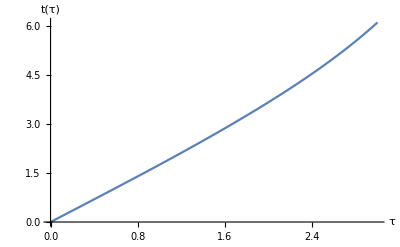
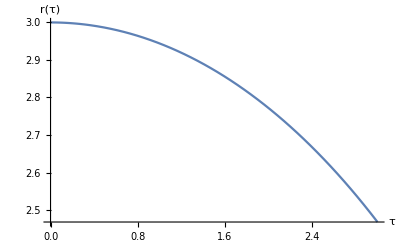

```mathematica
Geoplot[τ,init,vinit,{0,3},{t,r}]
```

NOTE: Geoplot requires a properly normalized vector to function.  For example:

```mathematica
Geoplot[τ,init,{4/(√(1-2/3)),0,0,0},{0,3},{t,r}]
```

Invalid timelike or null normilazation, 
or divergent Metric at initial point.

For time-like vectors we can input ("Max",dx^1/dτ,dx^2/dτ,dx^3/dτ) and have Geoplot properly normalize dx^0/dτ (NOTE:  the normalization must be accurate to 10^-10 precission). 

As an example we look at an object orbiting in the plane θ=π/2.

```mathematica
init={0,4,π/2,0};
```

```mathematica
vinit={"Max",0,0,1};
```

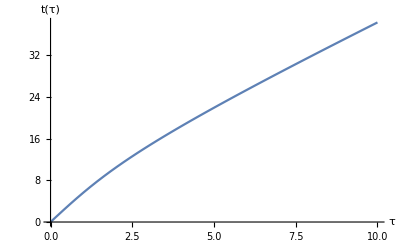
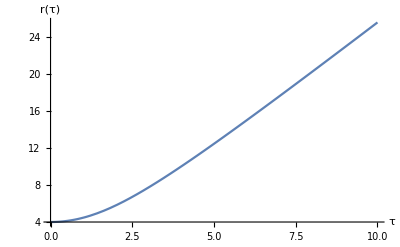
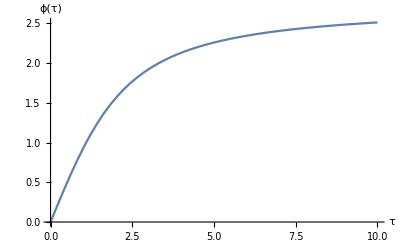

```mathematica
Geoplot[τ,init,vinit,{0,10},{t,r,ϕ}]
```

The normalization has been automatically done for us.  The text “Max” tells us to use the maximum solution, dx^0/dτ, of
-c^2-g_ij(dx^i/dτ dx^j/dτ )=(g_00(dx^0/dτ))^2+2g_(0i)(dx^i/dτ dx^0/dτ).
If we want the minimum solution one replaces “Max” with “Min”.

Once Geoplot has been used, an interpolation object called “GEOSOL” is created that contains the solutions to the geodesic equations.

```mathematica
GEOSOL
```

{{t→InterpolatingFunction[{{0., 10.}}, <>],r→InterpolatingFunction[{{0., 10.}}, <>],θ→InterpolatingFunction[{{0., 10.}}, <>],ϕ→InterpolatingFunction[{{0., 10.}}, <>]}}

“GEOSOL” be used to manipulate the numerical geodesic solutions.  For example, for the previous initial conditions, we can plot the particle trajectory in the x-y plane:

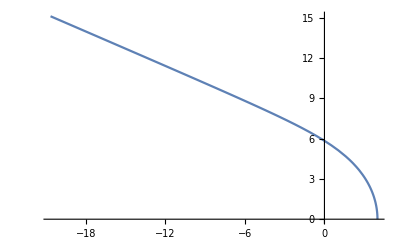

```mathematica
ParametricPlot[Evaluate[{r[τ] Cos[ϕ[τ]],r[τ] Sin[ϕ[τ]]}/.GEOSOL],{τ,0,10}]
```

```mathematica
Clear[M]
```

It is also usefull to have a function which checks wheter a specific x^μ(u) is a solution.  Issol[{x_0(u),x_1(u),x_2(u),x_3(u)},u] returns either True, False, or an expression which must be equal to zero if the four vector is to be a geodesic. Let us see if the trajectory
 x^μ(τ)={τ, R, π/2,0}  is a solution to the geodesic equation

```mathematica
Issol[{τ,R, π/2,0},τ]
```

(M^2 (-2 M+R)^2)/R^6

Thus x^μ is a solution if R=∞  (Note: R=2M should always be treated with care because the metric is singular in these coordinates. Any expression given by Issol that gives g(x^μ)=∞ should be checked clearly.)

```mathematica
?Issol
```

Issol[x[τ],τ] will give True if the four vector x[τ] is a solution to the geodesic equations and False otherwise. Issol may also give an expression which must be zero for x^μ to be a geodesic

DISCLAIMER: Issol is by no means perfect. If Issol gives false it does not mean your geodesic is not a solution it might mean that the program has not done enough simplifications or taken into account algebraic identities.

Finally

```mathematica
?ReplaceCoords
```

ReplaceCoords[exp,coords] replaces the default coordinates (COORDINATES) to thos specified in coords.

This function is usefull when wanting to input a particular value to your coordinates. For example

```mathematica
ReplaceCoords[GMET,{τ, R, π/2,0}]
```

{{-1+(2 M)/R,0,0,0},{0,R/(-2 M+R),0,0},{0,0,R^2,0},{0,0,0,R^2}}

```mathematica
ReplaceCoords[Christoffel[{{1},{1,1}}],{τ, R, π/2,0}]
```

M/(2 M R-R^2)

```mathematica
Christoffel[{{1},{1,1}}]
```

M/(2 M r-r^2)

# Covariant Derivatives and Tensor Definitions

The index structure in GRQUICK is {{top indices},{bottom indices}}.  For a purely covariant tensor one can use {bottom indices}, and for a pure contravariant one must use {{top indices},{}} (this will be fixed in the future).

We switch to our original spherical symmetric metric.

```mathematica
Metin[DiagonalMatrix[{m[t,r],n[t,r],r^2,r^2 Sin[θ]^2}],{t,r,θ,ϕ}]
```

Metric Success

Einstein[0,0] Re-Populates arrays

```mathematica
Einstein[0,0];
```

We calculate ∇_0 G_00

```mathematica
Coderv["Einstein",{0,0},0]
```

(m^(0,1)[t,r] n^(1,0)[t,r])/(r n[t,r]^2)+(2 m[t,r] (-n[t,r]+n[t,r]^2+r n^(0,1)[t,r]) n^(1,0)[t,r])/(r^2 n[t,r]^3)-(m[t,r] (-n^(1,0)[t,r]+2 n[t,r] n^(1,0)[t,r]+r n^(1,1)[t,r]))/(r^2 n[t,r]^2)

coderv also works with more complex tensor such as:

```mathematica
Coderv["Riemann",{{0},{1,0,1}},0]
```

-(m^(1,0)[t,r] (m[t,r] (m^(0,1)[t,r] n^(0,1)[t,r]+(n^(1,0)[t,r])^2)+n[t,r] ((m^(0,1)[t,r])^2+m^(1,0)[t,r] n^(1,0)[t,r]-2 m[t,r] (m^(0,2)[t,r]+n^(2,0)[t,r]))))/(2 m[t,r]^3 n[t,r])-(n^(1,0)[t,r] (m[t,r] (m^(0,1)[t,r] n^(0,1)[t,r]+(n^(1,0)[t,r])^2)+n[t,r] ((m^(0,1)[t,r])^2+m^(1,0)[t,r] n^(1,0)[t,r]-2 m[t,r] (m^(0,2)[t,r]+n^(2,0)[t,r]))))/(2 m[t,r]^2 n[t,r]^2)+1/(4 m[t,r]^2 n[t,r])(m^(1,0)[t,r] (m^(0,1)[t,r] n^(0,1)[t,r]+(n^(1,0)[t,r])^2)+m[t,r] (n^(0,1)[t,r] m^(1,1)[t,r]+m^(0,1)[t,r] n^(1,1)[t,r]+2 n^(1,0)[t,r] n^(2,0)[t,r])+n^(1,0)[t,r] ((m^(0,1)[t,r])^2+m^(1,0)[t,r] n^(1,0)[t,r]-2 m[t,r] (m^(0,2)[t,r]+n^(2,0)[t,r]))+n[t,r] (2 m^(0,1)[t,r] m^(1,1)[t,r]+n^(1,0)[t,r] m^(2,0)[t,r]+m^(1,0)[t,r] n^(2,0)[t,r]-2 m^(1,0)[t,r] (m^(0,2)[t,r]+n^(2,0)[t,r])-2 m[t,r] (m^(1,2)[t,r]+n^(3,0)[t,r])))

We now do a quick check of coderv.

```mathematica
check=(D[Riemann[{{0},{1,0,1}}],t]+
Sum[Christoffel[{{0},{0,ss}}] Riemann[{{ss},{1,0,1}}],{ss,0,3}]
-Sum[Christoffel[{{ss},{0,1}}]Riemann[{{0},{ss,0,1}}],{ss,0,3}]
-Sum[Christoffel[{{ss},{0,0}}]Riemann[{{0},{1,ss,1}}],{ss,0,3}]
-Sum[Christoffel[{{ss},{0,1}}]Riemann[{{0},{1,0,ss}}],{ss,0,3}]);
```

```mathematica
FullSimplify[Expand[check-Coderv["Riemann",{{0},{1,0,1}},0]]]
```

0

Along with the standard tensors we can define new tensors exactly the way one defines functions in mathematica (I am working on a define tensor function but for now this works).  Here is an example of a tensor definition of (G^μ)_ν:

```mathematica
Gupdn[{{a_},{b_}}]:=Sum[IMetric[a,jj]Einstein[jj,b],{jj,0,3}]
```

Now we can take covariant derivatives of the new object.

```mathematica
Coderv["Gupdn",{{0},{0}},0]
```

(m^(0,1)[t,r] n^(1,0)[t,r])/(r m[t,r] n[t,r]^2)+(2 (-n[t,r]+n[t,r]^2+r n^(0,1)[t,r]) n^(1,0)[t,r])/(r^2 n[t,r]^3)-(-n^(1,0)[t,r]+2 n[t,r] n^(1,0)[t,r]+r n^(1,1)[t,r])/(r^2 n[t,r]^2)

We now define a rank 2 contravariant tensor and take a covariant derivative (the bad notation for pure contravariant tensors will be fixed later).:

```mathematica
Gupup[{{a_,b_},{}}]:=Sum[IMetric[b,ss]Gupdn[{{a},{ss}}],{ss,0,3}]
```

```mathematica
Coderv["Gupup",{{0,0},{}},0]
```

(m^(0,1)[t,r] n^(1,0)[t,r])/(r m[t,r]^2 n[t,r]^2)+(2 (-n[t,r]+n[t,r]^2+r n^(0,1)[t,r]) n^(1,0)[t,r])/(r^2 m[t,r] n[t,r]^3)-(-n^(1,0)[t,r]+2 n[t,r] n^(1,0)[t,r]+r n^(1,1)[t,r])/(r^2 m[t,r] n[t,r]^2)

Finally for rank 2 covariant tensor we can take their trace as :

```mathematica
Tenstr["Einstein"]-Sum[Gupdn[{{aa},{aa}}],{aa,0,3}]
```

0

Vectors

Vectors have a special place in GRQUICK because one can either put them directly into “coderv” or functionally define them.

For example let us take ∇_0  x^0:

```mathematica
x={t,r,θ,ϕ}
```

{t,r,θ,ϕ}

```mathematica
X[a_]:=x[[a+1]]
```

NOTE: the +1 comes from the fact that we want the index to start at zero but mathematica starts the index at 1.

We can now take a covariant derivative in two ways:

```mathematica
Coderv["X",{{0},{}},0]
```

1+(r m^(0,1)[t,r])/(2 m[t,r])+(t m^(1,0)[t,r])/(2 m[t,r])

```mathematica
Coderv[{t,r,θ,ϕ},{{0},{}},0]
```

1+(r m^(0,1)[t,r])/(2 m[t,r])+(t m^(1,0)[t,r])/(2 m[t,r])

```mathematica
Coderv["X",{{0},{}},0]-Coderv[{t,r,θ,ϕ},{{0},{}},0]
```

0

NOTE: a vector in “coderv” is defined to be covariant or contravariant based solely on the input of the index structure. For example:

```mathematica
Coderv[{t,r,θ,ϕ},{0},0]
```

1+(r m^(0,1)[t,r])/(2 n[t,r])-(t m^(1,0)[t,r])/(2 m[t,r])

takes the input vector to be covariant

```mathematica
Clear[x,X]
```

Double Derivatives

Double (or higher) covariant derivatives require a bit more work to obtain but it’s not that bad. (Future work will automate higher covariant derivatives).

In order to show the abilities of GRQUICK we now switch to an arbritrary diagonal matrix (we dont use a fully arbritrary metric because it takes a fair amount of time and memory).

```mathematica
Metin[DiagonalMatrix[{f00[t,x,y,z],f11[t,x,y,z],f22[t,x,y,z],f33[t,x,y,z]}],{t,x,y,z}]
```

Metric Success

```mathematica
MatrixForm[GMET]
```

(f00[t,x,y,z] | 0 | 0 | 0
0 | f11[t,x,y,z] | 0 | 0
0 | 0 | f22[t,x,y,z] | 0
0 | 0 | 0 | f33[t,x,y,z])

For the new metric, we populate the relevant arrays

```mathematica
Einstein[0,0];
```

Now we define a vector and the covariant derivative of the vector: (R^s)_(a b v)

```mathematica
A={(t+x+y+z)^1,(t+x+y+z)^2,(t+x+y+z)^3,(t+x+y+z)^4}
```

{t+x+y+z,(t+x+y+z)^2,(t+x+y+z)^3,(t+x+y+z)^4}

```mathematica
Dvec[{v_,p_}]:=Coderv[A,{v},p]
```

Now we prove ∇_σ  ∇_p A_v -∇_p  ∇_σ A_v= A_s(R^s)_(v p σ)

```mathematica
FullSimplify[Table[(Coderv["Dvec",{v,p},σ]-Coderv["Dvec",{v,σ},p])
-Sum[A[[kk]] Riemann[{{kk-1},{v,p,σ}}],{kk,1,4}],{v,0,3},{p,0,3},{σ,0,3}]]
```

{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

These are all of the functions GRQUICK has.  Future plans include a define tensor function, which makes defining a tensor easier (i.e. implicit dummy summation) as well as a covariant derivative function which can take multiple co-derivatives.